## makes plots for SwarmControl.herokuapp.com Aaron Becker

## Shiva’s Automatic control

```mathematica
Clear[x]
D[1/2(sig - sig2[x])^2,x]
```

-(sig-sig2[x]) sig2'[x]

{200,150,100,50,20}

```mathematica
Max[x1]
```

866

```mathematica
x1= (*7 failes, 43 good*){111.325,111.353,116.213,103.159,128.895,124.903,132.160,123.347,112.272,134.835,160.774,106.715,117.534,125.966,133.198,131.955,162.866,136.751,124.908,153.207,165.725,173.752,209.02,192.293,182.62,112.473,111.029,118.395,119.095,154.619,120.945 ,102.479,107.198,123.327,140.435,102.084,123.86,128.308,115.009,94.817,113.622,137.534,129.824};
(*x1={416.96,107.909,114.931,128.945,156.857};*)
y1={200,200,200,200,200};
x2={82.097,189.448,137.459,174.661,63.84};
y2={150,150,150,150,150};
x3={40.192,109.181,71.028,111.348,62.024};
y3={100,100,100,100,100};
x4={52.953,33.51,31.631,55.114,94.96};
y4={50,50,50,50,50};
x5={52.566,41.306,43.943,33.132,43.992};
y5={20,20,20,20,20};
x=Reverse[{x1,x2,x3,x4,x5}];
y=Reverse[{y1,y2,y3,y4,y5}];
```

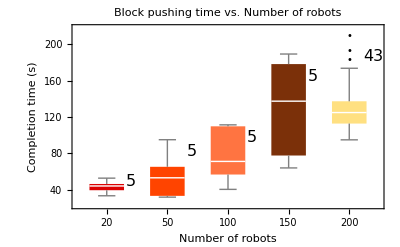

```mathematica
FontSz = 16;SetDirectory[NotebookDirectory[]];
BoxWhiskerChart[x ,{"Outliers",{"MedianMarker",1,Directive[Thick,White]}},ChartStyle->2,PlotTheme->"Scientific",
ChartLabels->Placed[{y⟦;;,1⟧,Length/@x},{Axis,{1.2,.8}}],
LabelStyle->{Black,FontFamily->"Times",FontSize->FontSz},
PlotLabel-> Style["Block pushing time vs. Number of robots",FontSize->FontSz],
ChartLabels->y⟦;;,1⟧,LabelStyle->FontSz,FrameLabel->{"Number of robots",StringForm[ "Completion time (s)"]}]
Export["../pictures/pdf/AutoControlVaryN.pdf",%];
```

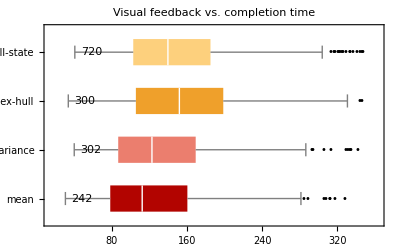

#### Circle Packing: finding the minimum variance is actually hard! http://www.math.ucsd.edu/~ronspubs/90_01_penny_packing.pdf

```mathematica
N[(2)^2/(2n)((√3 n^2)/(4 π)) /n]
```

0.275664

```mathematica
Clear[r]
(2)^2/(2n)((√3 n^2)/(4 π)) /n
```

(√3)/(2 π)

```mathematica
N[Solve[x + slope 200 r^2 == 2,x]]
```

{{x→1.44867}}

```mathematica
N[(1/4+slope {20,50,100,150,200} r^2),3]
N[(3/2+slope {20,50,100,150,200} r^2),3]
```

{0.305,0.388,0.526,0.663,0.801}

{1.56,1.64,1.78,1.91,2.05}

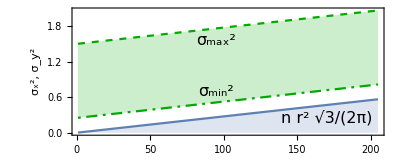

```mathematica
numMinMaxVar= {{200,3,7},{100,2,5},{50,2,3},{150,3,5},{20,0.5,2},{20,1.5,2},{20,2.5,2.6},{100,3,5}};
r = 1/10;(*r =the radius of our robots?*)
(*U = 1/d^2(∑^n)_(i=1)||pt-Mean(||)^2 in paper = (√3 n^2)/(4 π)*)
(*Var = 1/n(∑^n)_(i=1)(Subscript[x, i]-Subscript[Mean, y])^2 +1/n(∑^n)_(i=1)(Subscript[y, i]-Subscript[Mean, y])^2 in our code*)
(*   ((2r)^2 √3 n^2)/(2 n 4 π)*)
slope = (√3)/(2 π);
FontSz = 16;
DiscretePlot[{(2r)^2/(2n)((√3 n^2)/(4 π)), 1/4+slope n r^2,3/2+slope n r^2 },{n,1,205},Joined->True,Filling->{1-> Axis,3->{2}},PlotStyle->{Automatic,Directive[Darker[Green],Dashing[{.005,.01,0.02,0.01}]],Directive[Darker[Green],Dashed]},
Frame->{True,True,False,False},
LabelStyle->{Black,FontFamily->"Times",FontSize->FontSz},
FrameLabel->{"n, Number of Robots", "σ_x^2,    σ_y^2"},
AspectRatio->.4,
Epilog->{
xv =9;
Text[Style["σ_max^2",FontFamily->"Times",FontSize->FontSz],{95,1.56},Automatic,{xv,1}],
Text[Style["σ_min^2",FontFamily->"Times",FontSize->FontSz],{95,.7},Automatic,{xv,1}],
Text[Style["n r^2 √3/(2π)",FontFamily->"Times",FontSize->FontSz],{170,.25},Automatic,{xv,1}]
(*,PointSize->Large,
(*good values*)Green,Point[numMinMaxVar⟦;;,{1,2}⟧],
(*too big values*)Red,Point[numMinMaxVar⟦;;,{1,3}⟧]*)
}
(*,Epilog->{PointSize->Large,
(*good values*)Green,Point[numMinMaxVar⟦;;,{1,2}⟧],
(*too big values*)Red,Point[numMinMaxVar⟦;;,{1,3}⟧]
}*)
(*,PlotRange->{{0,155},{0,5}}*)
]
Export["../pictures/pdf/VarianceMinMaxBand2.pdf",%];
```

```mathematica
N[7/50]
```

0.14

```mathematica
(*too small values*)Blue, Point[{{20,1},{40,1},{50,1},{60,1},{100,2}}],
(*good values*)Green, Point[{{20,2.5}{40,2},{50,2},{60,2},{100,3}}],
(*too big values*)Red, Point[{{20,4},{40,4},{50,4},{60,4},{100,6}}]
```

-Robot radius is 0.1, -They are the min variances, for this maze and shape, I think some good values are like this : 20 -> too small : 1 good : 2.5 too big : 4
40 -> too small : 1 good : 2 too big : 4
50 -> too small : 1 good : 2 too big : 4
60 -> too small : 1 good : 2 too big : 4
100 -> too small : 2 good : 3 too big : 6

These numbers are experimental, but they are bigger for fewer numbers not to get stuck between mazes when one or two robots are stock.I think this is interesting.

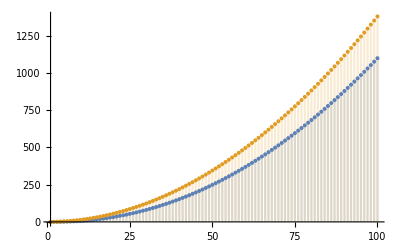

```mathematica
CircleMinVarianceLowerBound[n_]:=∑_(k=1)^n (√(3/16+(√3 (k-1))/(2 π))-(√3)/4)^2
DiscretePlot[{CircleMinVarianceLowerBound[n],(√3 n^2)/(4 π) },{n,1,100}]
```

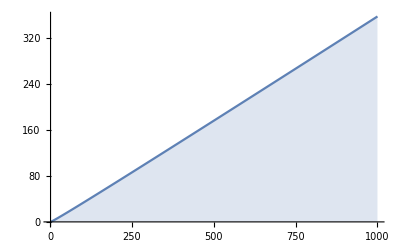

```mathematica
DiscretePlot[√CircleMinVarianceLowerBound[n],{n,1,100}]
```

```mathematica
Null
```

Null